# Mathematica Workbook 1

## Sinusoidal functions

## Preliminaries

This is your first Mathematica Workbook activity of the semester, and that means you will have to be patient with the software and with yourself.  The purposes of this workbook are:

To teach you about sinusoidal functions of a single independent variable, including their different parameterizations and their derivatives.

To teach you how to make, maniuplate and display graphs of one independent variable using Mathematica.

There are two kinds of content in this workbook, tutorials and activities.  In tutorials, you play with a simulation and answer questions.  In activities, you complete tasks and solve problems.  You will be able to recognize where you must enter preset input by the light red background.  You will recognize where you must create new input by the light blue background.  You will answer questions with text in light green boxes.

Here are a list of reminders about Mathematica that are critical for your success:

You enter a line of input by typing SHIFT - ENTER.  Any input you must enter will be highlighted with a

Syntax is critically important.  For example, you must pay attention to capitalization.

You can open "palettes" that allow you to insert certain symbols and commands with a click.  For starters, I recommend the "Basic Math Assistant"pallete.

Do not confuse parentheses ( ), square brackets [ ], and curly brackets { }.

When in doubt, look stuff up in the Documentation Center (under Help menu) and try to follow those examples.

Cutting and pasting input saves times and cuts down on typing errors.

Always type a space between symbols and you will reduce the number of mistakes you make immensely.

You will need to review these several times, because they are easy to forget.

All right!  Let's Go!

## Activity 1: Real simple plotting

Our first task is to learn how to plot (or graph) simple functions.  First, we meed to make a distinction between three types of variables: independent variables, dependent variables, and parameters.

Independent variable: In a simple Cartesian plot "y vs. x", this is the variable on the "x"-axis.  In Mathematica, to make a plot, you specifiy the domain of the independent vairable that you want to plot.

Dependent variable: In a simple Cartesian plot "y vs. x", this is the variable on the "y"-axis.  When making a graph in Mathematica, the dependent variable will often be written as a function of the independent variable and the parameters.

Parameter: This is any other number that is held at a fixed value when making a graph.  Changing parameters often changes the relative scale and location of the graph of a function, but keeps the same shape qualitatively.

For example, here is a graph of sine.  To make the graph, put you cursor on the line and hit SHIFT-ENTER



In the input expression above, notice several things.  The independent variable is ϕ, the dependent variable isn't named, but it is the function Sin[ϕ].  There are no parameters in this example.  In terms of input syntax, note that functions like Plot and Sin are capitalized and their arguments are surrounded by the square brackets.  The list that specifies the domain of the graph {ϕ,0,2π} uses curly brackets.  This is a general rule of syntax in Mathematica: lists uses curly brackets and functions use square brackets.

A.1.1: Now, in the space below, plot the cosine curve for the same domain of ϕ.  As a shortcut, cut and paste the input above and change the function.

```mathematica
Plot[Sin[ϕ],{ϕ,0,2π}]
```

-Graphics-

You can add options, here is an example:

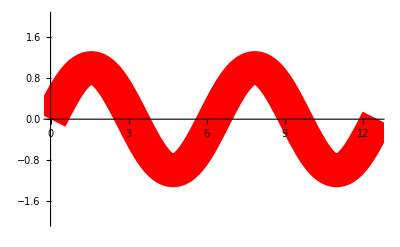

```mathematica
Plot[Sin[ϕ],{ϕ,0,4π}, PlotStyle->{Thickness[0.06],Red},PlotRange->{-2,2}]
```

When typing in input, the arrow after "PlotStyle" and "PlotRange" appears automatically if you type a dash "-" followed by ">".   "Thickness[0.02] is a function that tells Mathematica that the line should be 2% the thickness of the total plot.  I think.  "PlotRange" is followed by a list with the maximum and minimum y-values.

Plot has lots of options.  Highlight "Plot" in the input above and then click the F1 key.  Scroll down the help page that opens, look at the Basic Examples, and then look at some of the other options.

A.1.2: Now plot the prettiest cosine curve in the world.

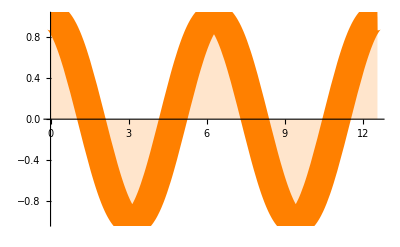

```mathematica
Plot[Cos[ϕ],{ϕ,0,4 π}, PlotStyle-> {Thickness[0.05],Orange},Filling->Axis]
```

## Tutorial 1: Real sinusoids with linear phase evolution

The phase of a sinusoid is often not the physical variable of interest.  For example, in simple harmonics oscillating systems the phase ϕ is a linear function of time.  The standard form for this is:

ϕ=ω t+ϕ_0

The variable ω is the angular frequency and the variable ϕ_0 is the phase constant.  To better understand this relationship between phase and time, play with the following simulation.  If you click on the little plus signs next to each parameter slider, the value taken by that parameter are shown.

```mathematica
Manipulate[Plot[ω t + ϕ0,{t,0,10},PlotRange->{-1,20}],{ω,1,5},{ϕ0,0,2π}]
```

T.1.1: What happens the graph when you increase the angular frequency ω?

the slope becomes steeper

T.1.2: What happens to the graph when you vary the phase constant ϕ_0?

the phase constant adjusts the y intercept of the graph and slides the graph up or down based on sign

Now lets put that expression for phase into the cosine function and define our dependent variable as a function of time:

y(t)=A cos(ω t + ϕ_0)

I have included one more parameter, the amplitude A, in this definition.  Play with the following manipulator that allows you to adjust the parameters for a fixed domain of the independent time variable.

```mathematica
Manipulate[Plot[A Cos[ω t + ϕ0],{t,0,10},PlotRange->{-5,5},AxesLabel->{t,y}],{ω,1,5},{ϕ0,0,2π},{A, 1, 4}]
```

T.1.3: Describe what happens as you increase the angular frequency ω.

Increasing the angular frequency pinches the graph or stretches it affecting frequency

T.1.4: Describe what happens as you increase ϕ_0.

increaseing the phase constant phi naught shifts the graph to the left by a factor of phi naught

T.1.5: Describe what happend as you increase A.

Increasing A stretches the amplitude and increases the maximum and minimum

Using the same manipulator above, confirm that the relationship between period T and angular frequency ω is given by

T=2π/ω

Remember, the period is the time interval it takes for the sinusoidal function to repeat itself, i.e. the time between crests or troughs.

## Activity 2: Equivalent Real Sinusoids

In this activity, you are going to use graphical methods to compare different sinusoidal functions.  To do this, we need to learn how to show two graphs on the same plot.  There are several ways to do this.  One way is to make two separate graphs using the Plot command and then combine them with a Show command.

To do this, first I make a graph of one function

1

2

0

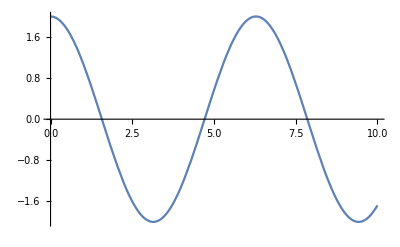

```mathematica
ω=1
A =2
ϕ0 = 0
graph1 = Plot[A Cos[ω t + ϕ0],{t,0,10}]
```

Notice this time, I did several new things.  First, in the input, I declared my parameters for amplitude, angular frequency and phase constant before I made the graph.  Also, I used an equal sign to give this graph a name "graph1".

Now I'll make a second graph.

2

1

π/3

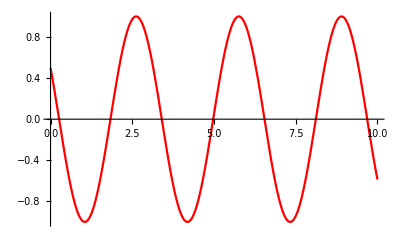

```mathematica
ω=2
A =1
ϕ0 = π/3
graph2 = Plot[A Cos[ω t + ϕ0],{t,0,10},PlotStyle->Hue[0]]
```

Notice that I changed the value for the paramters before I input the "graph2" command.  If I had done it in the reverse order, I would have gotten a different result.

I can combine these with the following input command.

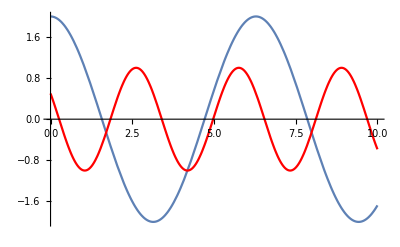

```mathematica
Show[graph1,graph2]
```

A.2.1: Okay, now that you know how to plot two functions on the same graph, use graphs to show that the following equation is true:

cosϕ=sin(ϕ+π/2)

In other words, if both graphs look exactly the same, then the equation is true.  Do this is the space provided below.

1

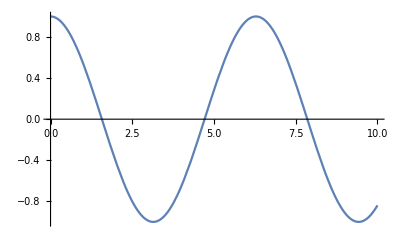

```mathematica
ω=1
graph = Plot[Cos[ω t],{t,0,10}]
graphsame = Plot[Sin[ω t+π/2], {t,0,10}]
Show[graph, graphsame]
```

A.2.2: Now show that

cos(ϕ+π/4)=-1/(√2)sinϕ+1/(√2)cosϕ

1

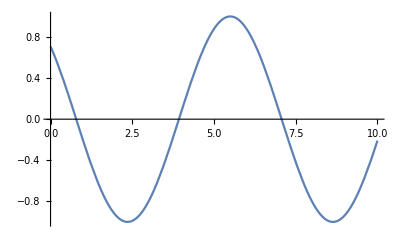

```mathematica
ω=1
graph = Plot[Cos[ω t+π/4],{t,0,10}]
graphsame = Plot[(-1/sqrt(2))Sin[ω t+π/2] +Cos[ω t] , {t,0,10}]
```

Let's end this section by showing you how to clear variables:

```mathematica
Clear[ω,A,ϕ0]
```

## Activity 3: Real Sinusoids Superposition with the Same Frequency

When you add together sinusoids with the same frequency, you get another sinusoid with the same frequency but different amplitude and phase constant.  Prove it!

A.3.1:  Make a manipulator that allows you to add together two sinusoids of the same frequency but variable amplitude and phase constant.  Use the same standard form for both real sinusoids.  Hint:  For simplicity, have one sinusoid with fixed parameters and the other one with variable.  Copy and paste some input code above as a short cut.

```mathematica
Manipulate[Plot[A Sin[t+ϕ0]+ Sin[t],{t,0,10},PlotRange->{-10,10}],{A,1,5},{ϕ0,0,2π}]
```

A.3.2:  Using the manipulator above, give the conditions on the amplitudes and phase constants necessary for totally constructive interference of the two sinusoids.

maximum amplitude is about 6 and minimum amplitude is about -6 and are found at multiples of 2pi, so 0, 2pi, 4pi etc.

A.3.3:  What conditions are necessary for totally destructive interference of the two sinusoids?

phase constants at multiples of pi and maximums and minimums found at about 4, and -4

## Tutorial 2: Data fitting, Part 1

The following list of numbers are real data for the vertical position of a spring vs. time for a mass on a spring.  In other words, this is a list of pairs of numbers.  In each pair, the first number is the time in seconds and the second number is the vertical displacement of the spring measured in centimeters.  You need to SHIFT-ENTER this data so the computer can use this information.

```mathematica
list1 = {{0,-0.03705},{0.03333,-0.04631},{0.06667,-0.05866},{0.1,-0.06484},{0.1333,-0.06638},{0.1667,-0.05866},{0.2,-0.05249},{0.2333,-0.04014},{0.2667,-0.02316},{0.3,-0.004631},{0.335,0.01698},{0.3683,0.03396},{0.4017,0.04786},{0.435,0.05557},{0.4683,0.06175},{0.5017,0.06792},{0.535,0.06484},{0.5683,0.05403},{0.6017,0.04168},{0.635,0.0247},{0.6683,0.007719},{0.7017,-0.009262},{0.735,-0.02933},{0.7683,-0.04477},{0.8017,-0.05403},{0.835,-0.06175},{0.8683,-0.06484},{0.9017,-0.06484},{0.935,-0.05866},{0.9683,-0.04631},{1.002,-0.03242},{1.035,-0.01698},{1.068,0.001544},{1.102,0.001544},{1.135,0.03859},{1.168,0.04786},{1.202,0.06175},{1.235,0.06638},{1.268,0.06484},{1.302,0.05866},{1.335,0.05094},{1.368,0.03551},{1.402,0.01853},{1.435,0.001544},{1.468,-0.01698},{1.502,-0.03396},{1.535,-0.04631},{1.568,-0.05866},{1.602,-0.06329},{1.635,-0.06484},{1.668,-0.06329},{1.702,-0.05557},{1.735,-0.04014},{1.768,-0.02624},{1.802,-0.007719},{1.835,0.01235},{1.868,0.02624},{1.902,0.04014},{1.935,0.05557},{1.968,0.06021},{2.003,0.06484},{2.037,0.06021},{2.07,0.05403},{2.103,0.04322},{2.137,0.02624},{2.17,0.01235},{2.203,-0.007719},{2.237,-0.0247},{2.27,-0.03705},{2.303,-0.05249},{2.337,-0.06175},{2.37,-0.06329},{2.403,-0.06484},{2.437,-0.06021},{2.47,-0.05094},{2.503,-0.03705},{2.537,-0.02007},{2.57,-0.001544},{2.603,0.01544},{2.637,0.03242},{2.67,0.04631},{2.703,0.05557},{2.737,0.06175},{2.77,0.06329},{2.803,0.05866},{2.837,0.05249},{2.87,0.03859},{2.903,0.02161},{2.937,0.001544},{2.97,-0.01235},{3.003,-0.03088},{3.037,-0.04631},{3.07,-0.05557},{3.103,-0.06175},{3.137,-0.06329},{3.17,-0.06175},{3.203,-0.05557},{3.237,-0.04631},{3.27,-0.03088},{3.303,-0.01389},{3.337,0.003087},{3.37,0.02161},{3.403,0.03396},{3.437,0.05094},{3.47,0.05712},{3.503,0.06175},{3.537,0.06175},{3.57,0.05866},{3.603,0.04786},{3.637,0.03396},{3.672,0.01853},{3.705,0},{3.738,-0.01698},{3.772,-0.03396},{3.805,-0.04631},{3.838,-0.05557},{3.872,-0.06175},{3.905,-0.06329},{3.938,-0.06175},{3.972,-0.05094},{4.005,-0.03859},{4.038,-0.0247},{4.072,-0.009262},{4.105,0.01235},{4.138,0.02933},{4.172,0.04014}};
```

Notice...no output.  That's what those semicolons at the end of each input line do.

To plot this kind of data, use the command ListPlot.  I will name this graph "fred"

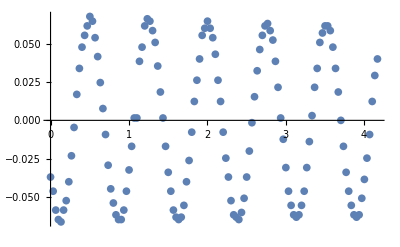

```mathematica
fred=ListPlot[list1]
```

Now I am going to insert "fred" into the previous manipulator with the domains of the variables adjusted to be sensible.

```mathematica
Manipulate[Show[fred,Plot[A Cos[ω t + ϕ0],{t,0,4.5}],PlotRange->{-.1,.1}],{ω,1,10},{ϕ0,0,2π},{A, .01, .1}]
```

T.2.1:  Using the manipulator, fit the experimental data to the standard sinusoidal form

y(t)=A cos(ω t + ϕ_0)

Remember, if you click on the "+" next to the slider you can see the parameter value.  For what values for the angular frequency ω, phase constant ϕ0 and amplitude A do you get the best fit?

8.28; 2.29965; 0.0664;

T.2.2:  How well does this function fit the real data?  Are there any obvious discrepencies?

The amplitude is fairly precise because the maximum and minimums are around .0664

## Activity 4: Data Fitting, Part II

In this activity, you are going to repeat the previous tutorial for new experimental data:

list2 describes the angular displacement of a pendulum

list3 describes the horizontal component of the position of an object in uniform circular motion.

To do this, follow these steps:

Make a ListPlot for each set of data.  Give each graph a different name

Make a manipulator for each set of data by copying the input code above.  You will have to change the name from "fred" to whatever your new names are.

The hard part: you will have to change the domain of the independent time variable and of the manipulated parameters.  To do this, first look at each ListPlot graph and estimate the time domian amplitude, and period.  You will use these value to adjust the range of variables in the manipulator.  Convert the period into the angular frequency using the relation at the end of Tutorial 1.  This will take some fiddling around.  Don't get frustrated...just try and figure it out by looking at the model and using the Documentation Center.

Here are the lists:

```mathematica
list2 = {{0,0.4135},{0.03333,0.449},{0.06667,0.4759},{0.1,0.4963},{0.1333,0.5014},{0.1667,0.4937},{0.2,0.4747},{0.2333,0.4478},{0.2667,0.4028},{0.3,0.3477},{0.335,0.2772},{0.3683,0.2122},{0.4017,0.1343},{0.435,0.05481},{0.4683,-0.0192},{0.5017,-0.1018},{0.535,-0.1692},{0.5683,-0.2421},{0.6017,-0.3028},{0.635,-0.3638},{0.6683,-0.4018},{0.7017,-0.4436},{0.735,-0.4666},{0.7683,-0.4853},{0.8017,-0.4885},{0.835,-0.4821},{0.8683,-0.4666},{0.9017,-0.4399},{0.935,-0.4005},{0.9683,-0.3481},{1.002,-0.2921},{1.035,-0.2273},{1.068,-0.1541},{1.102,-0.08239},{1.135,0.000698},{1.168,0.08611},{1.202,0.155},{1.235,0.2306},{1.268,0.2992},{1.302,0.3568},{1.335,0.4071},{1.368,0.4456},{1.402,0.4723},{1.435,0.4899},{1.468,0.5001},{1.502,0.4848},{1.535,0.4658},{1.568,0.4404},{1.602,0.3945},{1.635,0.3496},{1.668,0.2882},{1.702,0.2145},{1.735,0.1459},{1.768,0.06328},{1.802,-0.01904},{1.835,-0.09858},{1.868,-0.1686},{1.902,-0.2382},{1.935,-0.2975},{1.968,-0.3575},{2.003,-0.4042},{2.037,-0.4424},{2.07,-0.4614},{2.103,-0.4768},{2.137,-0.4949},{2.17,-0.4797},{2.203,-0.4603},{2.237,-0.431},{2.27,-0.3903},{2.303,-0.3496},{2.337,-0.2885},{2.37,-0.2238},{2.403,-0.1518},{2.437,-0.07105},{2.47,0.003348},{2.503,0.0777},{2.537,0.1522},{2.57,0.2245},{2.603,0.291},{2.637,0.3496},{2.67,0.4025},{2.703,0.4482},{2.737,0.4735},{2.77,0.4938},{2.803,0.495},{2.837,0.4836},{2.87,0.4695},{2.903,0.4325},{2.937,0.3892},{2.97,0.336},{3.003,0.2786},{3.037,0.2117},{3.07,0.1377},{3.103,0.05192},{3.137,-0.02187},{3.17,-0.09577},{3.203,-0.168},{3.237,-0.2375},{3.27,-0.2975},{3.303,-0.3601},{3.337,-0.403},{3.37,-0.4411},{3.403,-0.4589},{3.437,-0.4744},{3.47,-0.4821},{3.503,-0.4782},{3.537,-0.4603},{3.57,-0.4336},{3.603,-0.3891},{3.637,-0.3481},{3.672,-0.294},{3.705,-0.2245},{3.738,-0.1513},{3.772,-0.07989},{3.805,0.003446},{3.838,0.07793},{3.872,0.1522},{3.905,0.225},{3.938,0.2917},{3.972,0.3505},{4.005,0.3955},{4.038,0.4404},{4.072,0.466},{4.105,0.4786},{4.138,0.4862},{4.172,0.4785},{4.205,0.4554},{4.238,0.4314},{4.272,0.3872},{4.305,0.3324},{4.338,0.273},{4.372,0.2033},{4.405,0.1346},{4.438,0.06051},{4.472,-0.01636},{4.505,-0.09615},{4.538,-0.1708},{4.572,-0.2375},{4.605,-0.3055},{4.638,-0.3586},{4.672,-0.403},{4.705,-0.4374},{4.738,-0.4578},{4.772,-0.4754},{4.805,-0.4768},{4.838,-0.4719},{4.872,-0.4539},{4.905,-0.4272},{4.938,-0.384},{4.972,-0.3354},{5.005,-0.2831},{5.038,-0.2203},{5.072,-0.148},{5.105,-0.0764},{5.138,0.0063},{5.172,0.08055},{5.205,0.1518},{5.238,0.2278},{5.272,0.2903},{5.305,0.3477},{5.34,0.4002},{5.373,0.4378},{5.407,0.4632},{5.44,0.4797},{5.473,0.4835},{5.507,0.4783},{5.54,0.4554},{5.573,0.4257},{5.607,0.3838},{5.64,0.3333},{5.673,0.2709},{5.707,0.1982},{5.74,0.1374},{5.773,0.04911},{5.807,-0.0192},{5.84,-0.09896},{5.873,-0.1763},{5.907,-0.234},{5.94,-0.2921},{5.973,-0.3496},{6.007,-0.3941},{6.04,-0.431},{6.073,-0.4564},{6.107,-0.473},{6.14,-0.4782},{6.173,-0.473},{6.207,-0.4476},{6.24,-0.4196},{6.273,-0.3825},{6.307,-0.337},{6.34,-0.2822},{6.373,-0.219},{6.407,-0.1457},{6.44,-0.07325},{6.473,0.0063},{6.507,0.0834},{6.54,0.1553},{6.573,0.2295},{6.607,0.2868},{6.64,0.3496},{6.673,0.3945},{6.707,0.434},{6.74,0.4594},{6.773,0.4761},{6.807,0.4874},{6.84,0.4785},{6.873,0.4467},{6.907,0.4161},{6.94,0.3802},{6.973,0.3324},{7.008,0.2765},{7.042,0.1977},{7.075,0.1317},{7.108,0.05192},{7.142,-0.02772},{7.175,-0.09896},{7.208,-0.1686},{7.242,-0.241},{7.275,-0.2948},{7.308,-0.3523},{7.342,-0.4005},{7.375,-0.4323},{7.408,-0.4578},{7.442,-0.4655},{7.475,-0.4719},{7.508,-0.4694}};
```

```mathematica
list3 = {{0,-0.3705},{0.03333,-0.3242},{0.06667,-0.2779},{0.1,-0.1158},{0.1333,0.09262},{0.1667,0.2084},{0.2,0.2779},{0.2333,0.44},{0.2667,0.5326},{0.3,0.5859},{0.335,0.5621},{0.3683,0.4631},{0.4017,0.3242},{0.435,0.2084},{0.4683,0.1852},{0.5017,0.04631},{0.535,-0.2084},{0.5683,-0.3473},{0.6017,-0.44},{0.635,-0.5094},{0.6683,-0.5094},{0.7017,-0.5557},{0.735,-0.5326},{0.7683,-0.3705},{0.8017,-0.2547},{0.835,-0.1621},{0.8683,-0.04631},{0.9017,0.09262},{0.935,0.2779},{0.9683,0.3937},{1.002,0.44},{1.035,0.5094},{1.068,0.2779},{1.102,0.5557},{1.135,0.6947},{1.168,0.3473},{1.202,0.2779},{1.235,0.04631},{1.268,-0.1158},{1.302,-0.2084},{1.335,-0.3473},{1.368,-0.4863},{1.402,-0.5094},{1.435,-0.5326},{1.468,-0.5326},{1.502,-0.44},{1.535,-0.3705},{1.568,-0.2547},{1.602,-0.09262},{1.635,0},{1.668,0.1389},{1.702,0.3473},{1.735,0.44},{1.768,0.4863},{1.802,0.5789},{1.835,0.5094},{1.868,0.4168},{1.902,0.44},{1.935,0.301},{1.968,0.1357},{2.003,-0.006616},{2.037,-0.1621},{2.07,-0.2547},{2.103,-0.4168},{2.137,-0.4631},{2.17,-0.5094},{2.203,-0.5557},{2.237,-0.44},{2.27,-0.4168},{2.303,-0.3705},{2.337,-0.1621},{2.37,-0.04631},{2.403,0.04631},{2.437,0.2084},{2.47,0.3473},{2.503,0.4631},{2.537,0.5326},{2.57,0.5326},{2.603,0.5094},{2.637,0.4631},{2.67,0.3473},{2.703,0.2316},{2.737,0.1158},{2.77,-0.04631},{2.803,-0.1621},{2.837,-0.301},{2.87,-0.4631},{2.903,-0.5557},{2.937,-0.5094},{2.97,-0.4863},{3.003,-0.5094},{3.037,-0.3705},{3.07,-0.2316},{3.103,-0.1158},{3.137,0},{3.17,0.1158},{3.203,0.2316},{3.237,0.3705},{3.27,0.4863},{3.303,0.5094},{3.337,0.5326},{3.37,0.4631},{3.403,0.44},{3.437,0.3473},{3.47,0.1621},{3.503,0.06947},{3.537,-0.04631},{3.57,-0.2084},{3.603,-0.3705},{3.637,-0.4286},{3.672,-0.4998},{3.705,-0.5326},{3.738,-0.5094},{3.772,-0.44},{3.805,-0.3242},{3.838,-0.2316},{3.872,-0.1158},{3.905,0},{3.938,0.1852},{3.972,0.3473},{4.005,0.3937},{4.038,0.44},{4.072,0.5557},{4.105,0.5789},{4.138,0.4168},{4.172,0.2547}};
```

A.4.1: Use the manipulator to fit the list2 data in the space below, enter your answers in the text block below that:

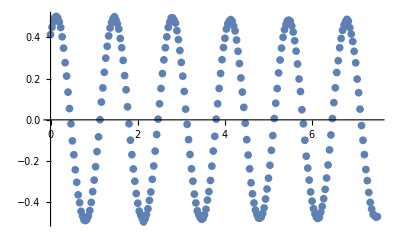

```mathematica
sally=ListPlot[list2]
Manipulate[Show[sally,Plot[A Cos[ω t + ϕ0],{t,0,8}],PlotRange->{-.5,.5}],{ω,1,10},{ϕ0,0,2π},{A, .05, .5}]
```

A.4.2: Use the manipulator to fit the list3 data in the space below, enter your answers in the text block below that:

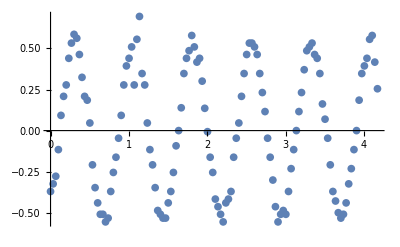

Show::gtype: Symbol is not a type of graphics.

```mathematica
susan = ListPlot[list3]
Manipulate[Show[susan,Plot[A Cos[ω t + ϕ0],{t,0,5}],PlotRange->{-.7,.7}],{ω,1,10},{ϕ0,0,2π},{A, .07, .7}]
```

## Tutorial 3: Functions and Derviatives of Sinusoids

Mathematica doesn't just make graphs.  It can do symbolic calculations, too.  Let's define the function

y(t)=A cos(ω t + ϕ_0)

using Mathematica in the simplest way possible

```mathematica
y[t_]=A Cos[ω t + ϕ0]
```

A Cos[ϕ0+t ω]

In this format, we have defined the function y(t) using square brackets, just like the sine and cosine functions that are built into Mathematica

Let's see whether this function works the way we think it should:

```mathematica
y[t]
y[t+T]
y[0]
y[2 π/ω]
```

A Cos[ϕ0+t ω]

A Cos[ϕ0+(t+T) ω]

A Cos[ϕ0]

A Cos[ϕ0]

We can use this function to understand why the formula

T=2π/ω

is the correct formula for the period.  The double equal sign "==" asks Mathematica "Is this true?"

```mathematica
y[t]==y[t+2 π/ω]
```

y[t]==y[t+(2 π)/ω]

Mathematica doesn't answer the question unless we tell it to "Simplify" the question.

```mathematica
Simplify[y[t]==y[t+2 π/ω]]
```

y[t]==y[t+(2 π)/ω]

T.3.1: In words, why is this equation true?

The equation is true because y(4pi/omega) takes the position on the unit circle a multiple of 2pi and starts off at that position and revolves back to it over the period of the oscillation.

Now let's take the derivative of our function with respect to time and define a new function:

```mathematica
vy[t_]=D[y[t],t]
```

y'[t]

I called this function "vy" because if y represents the displacement of an oscillator, its derivative with respect to time would be the oscillator's velocity in the y-direction

T.3.2: What is the amplitude of the velocity?

|-omega*A|

T.3.3: How does the phase of the velocity compare to the phase of the displacement?  In otherwords, what fraction of a period separates the maximum in velocity and the maximum in position?

1/2

T.3.3: How does the pattern change as you vary the phase constants?

changing the phase constants will shift the graph to the left or right by a multiple of the phase constant it wont change the relationship between velocity and maximum position

That last question may be easier if you take a look at the following graph

```mathematica
Manipulate[Plot[{A Cos[ω t + ϕ0],-A ω Sin[ϕ0+t ω]},{t,0,10},PlotRange->{-5,5},PlotStyle->{{Black,Thick},{Green, Thick}},AxesLabel->{t,""}],{ω,1,5},{ϕ0,0,2π},{A, 1, 4}]
```

## Activity 5: Derviative and Phases

When you add together sinusoids with the same frequency, you get another sinusoid with the same frequency but different amplitude and phase constant.  Prove it!

A.5.1:  Define a new function ay[t] that is the second derviative of the displacement y[t] from last section (aka the acceleraion of the oscillator).

```mathematica
ay[t_]=-(ω^2)A Cos[ω t + ϕ0]
```

-A ω^2 Cos[ϕ0+t ω]

A.5.2:  Now use Mathematica to convince yourself (and me) that the acceleration and positon are π radians (180 degrees, half a cycle) out of phase.

```mathematica
ω =1
A = 2
 ϕ0 = pi/2
pos = ACos[ω t + ϕ0]
a =Plot[ay[t_], {t, 0 , 10}]
x = Plot[pos, {t,0,10}]
Show[a,x]|
```

1

2

pi/2

ACos[pi/2+t]

## Tutorial 4: Phasors: The Complex Representation of Sinusoids

There is another way to represent sinusoidal functions of time called the phasor representation.  It emphasizes the connection between uniform circular motion and sinusoidal functions.  It also is connected with a brach of mathematics called complex numbers.  Instead of representing the sinusoidal function by a graph, the function is represented by an arrow.

Enter the input code below.  It defines four graphics objects that we can play with to visualize complex numbers and phasors.

```mathematica
phasor[z_,origin_,color_]:=Graphics[{color,Arrowheads[Large],Thick,Arrow[{origin,{Re[z]+origin[[1]],Im[z]+origin[[2]]}}]}]
phasorxcomp[z_,origin_,color_]:=Graphics[{color,Thick,Arrow[{origin,{Re[z]+origin[[1]],origin[[2]]}}],Text[Re[z],{Abs[z]/2, -Abs[z]/10}]}]
phasorycomp[z_,origin_,color_]:=Graphics[{color,Thick,Arrow[{origin,{origin[[1]],Im[z]+origin[[2]]}}],Text[Im[z],{-Abs[z]/10,Abs[z]/2}]}]
phasorgrid[max_]:=Graphics[{Arrowheads[Small],Thin,Arrowheads[{-.02,.02}],Arrow[{{-max,0},{max,0}}],Arrow[{{0,-max},{0,max}}],Text[Style["Real",Medium], {1.8,.2}],Text[Style["Imaginary",Medium], {.4,1.8}]}]
```

Using these structures, we can explore phasors.  First, input this manipulator.

```mathematica
Manipulate[Show[phasor[A ⅇ^(ⅈ ϕ),{0,0},Green],phasorxcomp[A ⅇ^(ⅈ ϕ),{0,0},Red], phasorycomp[A ⅇ^(ⅈ ϕ),{0,0},Purple],phasorgrid[2.2]],{A,.2,2},{ϕ,0,2π}]
```

In this diagram, the amplitude A is the size of the green arrow and the phase ϕ is the angle between the green arrow and the axis labeled "Real".  This is sometimes called the polar notation for a complex number: every complex number can be written like

z=Aⅇ^ⅈϕ

In this expression, "ⅇ" is Euler's constant and ⅈ = √-1.  A is the magnitude (or absolute value) of the complex number, and ϕ is the phase (or argument) of the complex number.  There is a lot of cool stuff here that I'm not going to go into but you can read about in your book.  Note that Euler's relation tells us

ⅇ^ⅈϕ=cosϕ+ⅈsinϕ

T.4.1 What do the red and purple arrows and numbers represent?

The red and purple arrows represent Real and imagainary solution vectors in (x,yi) space where the sum x+yi is the complex solution

Now we will animate the phasor and show the connection with sinusoidal math.  We will consider the case that the phase changes linearly with time like before:

ϕ=ω t+ϕ_0

Then the complex number is a function of time:

z(t)=A ⅇ^(ⅈ(ω t +ϕ_0))

Now...let's manipulate this expression:

```mathematica
Manipulate[Animate[Show[phasor[A ⅇ^(ⅈ ( ω t +ϕ0)),{0,0},Green],phasorxcomp[A ⅇ^(ⅈ ( ω t +ϕ0)),{0,0},Red], phasorycomp[A ⅇ^(ⅈ ( ω t +ϕ0)),{0,0},Blue],phasorgrid[2.2]],{t,0,2π/.1}],{{A,1},.1,2},{ω,.1,1},{ϕ0,0,2π}]
```

Play around with the parameters.  You can slow down the animation speed with the controls.

T.4.2 What happens to the arrows as the value of the angular frequency ω is increased?

the arrows rotate in the time t, at a faster speed

T.4.3 What happens as you change the phase constant ϕ_0?

changing the phase constant selescts the origin of location of the start of motion

Finally, run this last simulation.  The phasor diagram is inset into a graph that shows how the real part evolves in time for the given parameters. The first input give the parameters (which you can adjust if you like) and the second part of the input is the code for the animation.

```mathematica
A=2;
ω=.2;
ϕ0 = π/3;
```

```mathematica
Animate[Show[GraphicsArray[{{Show[phasor[A ⅇ^(ⅈ ( ω t +ϕ0)),{0,0},Green],phasorxcomp[A ⅇ^(ⅈ ( ω t +ϕ0)),{0,0},Red],phasorgrid[2.2]]},{Rotate[Plot[A Cos[ω u+ϕ0],{u,0,t+0.001},PlotRange->{{0,2π/.1},{-A*1.1,A*1.1}},ImageSize->220],-π/2]}}]],{t,0,2π/.1}]
```

Let's clear variables again.

```mathematica
Clear[ω,A,ϕ0]
```

## Activity 6: Taylor Expansions

The Taylor expansion of the sine function is

sinθ=θ-1/(3!)θ^3+1/(5!)θ^5-1/(7!)θ^7...

A.6.1: Use Mathematica to make a visual argument that as θ gets bigger, you need more an more terms of the Taylor expansion to get an accurate approximation.

```mathematica
Manipulate[Plot[A Sin[ω t],{t,0,10},PlotRange->{-5,5},AxesLabel->{t,y}],{ω,1,5},{A, 1, 4}]
"So if you notice the graph below, as theta increases in size, the pinch becomes greater as the frequency becomes smaller. As you slide the omega, and increase its value you'll notice the pinch as frequency increases, sliding omega back to smaller values getting closer to zero will yield a smaller theta and a larger frequency. This approximation altough still inaccurate is closer to the accurate approximation of 0 than larger values of theta because of these intersections. When theta is 0, theta has the most accurate approximation."
```

So if you notice the graph below, as theta increases in size, the pinch becomes greater as the frequency becomes smaller. As you slide the omega, and increase its value you'll notice the pinch as frequency increases, sliding omega back to smaller values getting closer to zero will yield a smaller theta and a larger frequency. This approximation altough still inaccurate is closer to the accurate approximation of 0 than larger values of theta because of these intersections. When theta is 0, theta has the most accurate approximation.

A.6.2 How many terms do you need if you want to have a polynomial that approximates a whole period well?

An infinite number of terms would yield the most accurate approximation of a whole period ignoring phasing.

## Activity 7: Bode Plots

A transfer function is the ratio of a complex output variable (like output voltage in an AC circuit) to the complex input variable (like input voltage in an AC circuit).  It is often written as a function.

H(ω)=(V_out(ω))/(V_in(ω))

A Bode Plot is a combination of graphs of a tranfer function.  Traditionally the top graph is log of H (ω) vs log f (or log ω) and the bottom graph is of the phase of H (ω), arctan (Im[H (ω)]/Re[H (ω)]) vs f or ω.  Remember that
frequency f and angular frequency ω are related by ω = 2 π f.  The Mathematica function BodePlot[g], where g is the tranfer function, can be used to make Bode Plots.  Mathematica expects the function g to be written in terms of 
the variable s, which equals i ω t.  As an example, the transfer function of a low pass filter is

H(ω)=1/(1+i ω/ω_lo)

We can graph this with the function BodePlot as

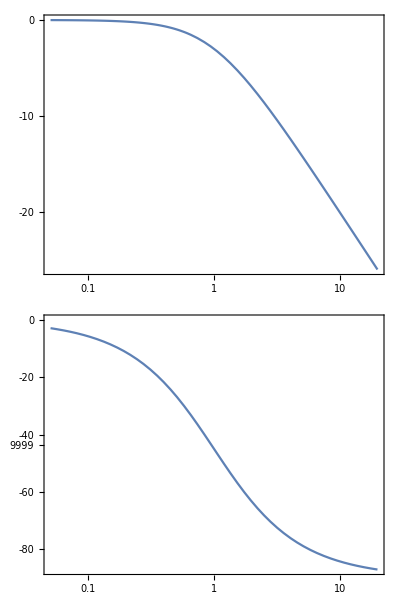

```mathematica
Subscript[ω, lo]=1;
BodePlot[1/(1+s/Subscript[ω, lo])]
```

```mathematica
Manipulate[BodePlot[1/(1+s/ω),PlotRange->{{{0.01,1000},Automatic},{{0.01,1000},Automatic}}],{ω,0.01,1000}]
```

The transfer function of a high pass filter is

H(ω)=(i ω)/(ω_hi+i ω)

A.8.1: Use the Mathematica function BodePlot[g] to make a Bode Plot of a high pass filter.

```mathematica
Manipulate[BodePlot[s/(ω +s),PlotRange->{{{0.01,1000},Automatic},{{0.01,1000},Automatic}}],{ω,0.01,1000}]
```

A.8.2: Use the Mathematica function BodePlot[g] to make a Bode Plot of a band pass filter, which has the transfer function of a low pass filter multiplied by a high pass filter.  Make a slider to investigate what happens as the
paramters ωlo and ωhi are changed.

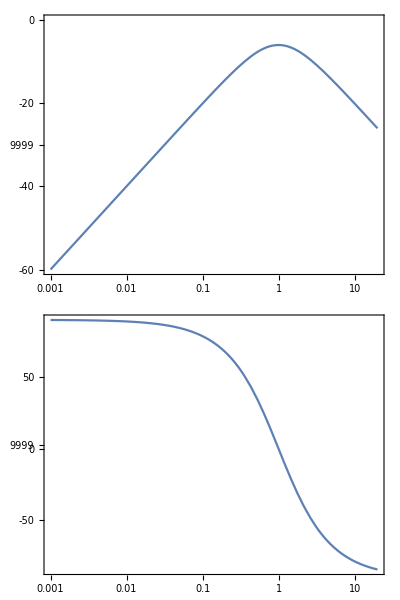

```mathematica
ωlo=1;
ωhi = 1; 
BodePlot[1/(1+s/Subscript[ω, lo])(s/(ωhi +s))]
Manipulate[BodePlot[1/(1+s/ωlo)(s/(ωhi +s)),PlotRange->{{{0.01,1000},Automatic},{{0.01,1000},Automatic}}],{ωhi,"ωlo,"0.01,1000}]
```